## κ invariance

### Nucleon part

```mathematica
(*TeX output*)
expr00=ALPNNcoupling/.{DD->D,DDs->Subscript[D, s],cG->Subscript[c, G],κd->Subscript[κ, d],κu->Subscript[κ, u],π0ALP->Subscript[θ, πa],ηprALP->Subscript[θ, η'a],ηALP->Subscript[θ, ηa]};
expr00=Simplify[D[expr00,#]#]&/@{Subscript[κ, u],Subscript[κ, d],Subscript[θ, πa],Subscript[θ, ηa],Subscript[θ, η'a]}//Total
expr00//TeXForm
```

(ϵ (4 D_s+3 D-F) θ_(a η'))/(2 √3)+ϵ c_G κ_d (F-D)+2 F ϵ c_G κ_u+(ϵ θ_ηa (D_s+2 F))/(√6)+1/2 ϵ (D+F) θ_πa

\frac{\epsilon  \left(4 D_s+3 D-F\right) \theta _{a \eta '}}{2 \sqrt{3}}+\epsilon  c_G \kappa _d (F-D)+2 F \epsilon  c_G \kappa _u+\frac{\epsilon  \theta _{\text{$\eta $a}} \left(D_s+2 F\right)}{\sqrt{6}}+\frac{1}{2} \epsilon 
   (D+F) \theta _{\text{$\pi $a}}

```mathematica
expr00=test1/.{mηpr^2->M2relationPureChPT["η'"]}/.{δ->0}/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}/.{DD->D,DDs->Subscript[D, s],cG->Subscript[c, G],mη->Subscript[m, η],mπ0->Subscript[m, π],ma->Subscript[m, a],mηpr->Subscript[m, η']}//Simplify
expr00//TeXForm
```

(ϵ c_G (m_π^2-m_η^2) (m_a^2 (3 D_s+2 D)-2 m_η^2 (2 D_s+D+F)+m_π^2 (D_s+2 F)))/((m_a^2-m_η^2) (m_a^2-m_η'^2))

\frac{\epsilon  c_G \left(m_{\pi }^2-m_{\eta }^2\right) \left(m_a^2 \left(3 D_s+2 D\right)-2 m_{\eta }^2 \left(2 D_s+D+F\right)+m_{\pi }^2 \left(D_s+2 F\right)\right)}{\left(m_a^2-m_{\eta }^2\right) \left(m_a^2-m_{\eta
   '}^2\right)}

```mathematica
expr00=δ*D[test1,δ]/.{mηpr^2->M2relationPureChPT["η'"]}/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}/.{DD->D,DDs->Subscript[D, s],cG->Subscript[c, G],mη->Subscript[m, η],mπ0->Subscript[m, π],ma->Subscript[m, a],mηpr->Subscript[m, η']}//Simplify
expr00//TeXForm
```

(δ m_π^2 ϵ c_G (D+F) (m_π^2-m_η^2) (m_a^2-2 m_η^2+m_π^2))/((m_π^2-m_a^2) (m_a^2-m_η^2) (m_a^2-m_η'^2))

\frac{\delta  m_{\pi }^2 \epsilon  c_G (D+F) \left(m_{\pi }^2-m_{\eta }^2\right) \left(m_a^2-2 m_{\eta }^2+m_{\pi }^2\right)}{\left(m_{\pi }^2-m_a^2\right) \left(m_a^2-m_{\eta }^2\right) \left(m_a^2-m_{\eta '}^2\right)}

### Tensor part

```mathematica
expr2=LagrangianTalp/.rulem0aTransformationSymbolic;
indiceslist={μ,ν,α,β,γ,δ,ρ,σ,ϵ};
expr3=(expr2/.{alp[x]->0,dalp[x,a_]:>0})+alp[x]*(D[expr2,alp[x]]/.{alp[x]->0,dalp[x,a_]:>0})+Sum[dalp[x,i]*(D[expr2,dalp[x,i]]/.{alp[x]->0,dalp[x,a_]:>0}),{i,indiceslist}]-ma^2/2 alp[x]^2+dalp[x,μ]^2/2;
expr4=(expr3/.{ϵ->0})+ϵ*(D[expr3,ϵ]/.{ϵ->0});
expr5=((expr4/.{δ->0})+δ*(D[expr4,δ]/.{δ->0}));
TotalLagrangianScaled=Expand[expr5]/. repsIndividual;
```

#### κ independence

```mathematica
exprr=LagrangianGivenFields[{"f_2","a","π^0"},{1,1,1}];
exprr=exprr/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
exprr=D[exprr,κu]κu+D[exprr,κd]κd//Simplify
exprr
```

0

0

### Scalar part

```mathematica
expr2=LscalarALP/.rulem0aTransformationSymbolic;
indiceslist={μ,ν,α,β,γ,δ,ρ,σ,ϵ};
expr3=(expr2/.{alp[x]->0,dalp[x,a_]:>0})+alp[x]*(D[expr2,alp[x]]/.{alp[x]->0,dalp[x,a_]:>0})+Sum[dalp[x,i]*(D[expr2,dalp[x,i]]/.{alp[x]->0,dalp[x,a_]:>0}),{i,indiceslist}]-ma^2/2 alp[x]^2+dalp[x,μ]^2/2;
expr4=(expr3/.{ϵ->0})+ϵ*(D[expr3,ϵ]/.{ϵ->0});
expr5=((expr4/.{δ->0})+δ*(D[expr4,δ]/.{δ->0}));
TotalLagrangianScaled=Expand[expr5]/. repsIndividual;
```

#### κ invariance

1

```mathematica
test1=LagrangianGivenFields[{"a","f_0","π^0"},{1,1,1}]//Simplify;
test1=test1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
test1=D[test1,κu]κu+D[test1,κd]κd//Simplify
{#,D[test1,#]}&/@{CoefA,CoefB,CoefC,CoefD}
```

0

(CoefA | 0
CoefB | 0
CoefC | 0
CoefD | 0)

2

```mathematica
test1=FeynmanRuleVertex[{"a","κ^0","(K̄)^0"},{1,-1,-1},{"a","κ","π"}]//Simplify;
test1=test1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
test1=D[test1,κu]κu+D[test1,κd]κd//Simplify;
{#,D[test1,#]}&/@{CoefA,CoefB,CoefC,CoefD}
```

(CoefA | 0
CoefB | 0
CoefC | 0
CoefD | 0)

### VMD part

```mathematica
expr2=VMDtermALP/.rulem0aTransformationSymbolic;
indiceslist={μ,ν,α,β,γ,δ,ρ,σ,ϵ};
expr3=(expr2/.{alp[x]->0,dalp[x,a_]:>0})+alp[x]*(D[expr2,alp[x]]/.{alp[x]->0,dalp[x,a_]:>0})+Sum[dalp[x,i]*(D[expr2,dalp[x,i]]/.{alp[x]->0,dalp[x,a_]:>0}),{i,indiceslist}]-ma^2/2 alp[x]^2+dalp[x,μ]^2/2;
expr4=(expr3/.{ϵ->0})+ϵ*(D[expr3,ϵ]/.{ϵ->0});
expr5=((expr4/.{δ->0})+δ*(D[expr4,δ]/.{δ->0}));
TotalLagrangianScaled=Expand[expr5]/. repsIndividual;
```

#### κ invariance

```mathematica
mell2=LagrangianGivenFields[{"a","ρ^0","A"},{1,1,1}]//Simplify;
mell2=mell2/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
mell2=D[mell2,κu]κu+D[mell2,κd]κd//Simplify;
mell=LagrangianGivenFields[{"a","ρ^0","ρ^0"},{1,1,1}]//Simplify;
mell=mell/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
mell=D[mell,κu]κu+D[mell,κd]κd//Simplify;
mell3=LagrangianGivenFields[{"a","π^+","π^-","π^0"},{1,1,1,1}]//Simplify;
mell3=mell3/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
mell3=D[mell3,κu]κu+D[mell3,κd]κd//Simplify;
mell4=LagrangianGivenFields[{"ρ^+","π^+","a"},{1,1,1}]//Simplify;
mell4=mell4/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
mell4=D[mell4,κu]κu+D[mell4,κd]κd//Simplify;
mell
mell2
mell3
mell4
```

0

0

0

«1 more identical outputs»

### Kaon decay part

#### Kinematics

```mathematica
particleslist["K^0π^0"]={"K^0","π^0"};
particleslist["(K̄)^0π^0"]={"(K̄)^0","π^0"};
particleslist["K^+π^-"]={"K^+","π^-"};
particleslist["K^-π^+"]={"K^-","π^+"};
particleslist["ηK^0"]={"η","(K̄)^0"};
particleslist["η'K^0"]={"η'","(K̄)^0"};
proclistKπ={"K^0π^0","(K̄)^0π^0","K^+π^-","K^-π^+","ηK^0","η'K^0"};
Do[
prgroupname[proc]="Kπ";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclistKπ}];
Do[
labelList[proc]={"K","π"};
Sfactor[proc]=1;
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,proclistKπ}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct2body[i,j],{i,1,2,1},{j,i,2,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,2,1}]
]
,{proc,proclistKπ}]
```

{Null,Null,Null,Null,Null,Null}

#### κ independence

```mathematica
Do[
melelement[process]=ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process]//Simplify;
melelementExplicit[process]=melelement[process]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
melementκ[process]=Simplify[D[melelementExplicit[process],κu]*κu]+Simplify[D[melelementExplicit[process],κd]*κd](*/.{mK0^2->M2relationPureChPT["K^0"],mKplus^2->M2relationPureChPT["K^0"],mηpr^2->M2relationPureChPT["η'"]}*)//ruleLeadingOrderIsospin//Together//Simplify
,{process,proclistKπ}]
Print["κ-dependent parts:"]
{#,melementκ[#]}&/@proclistKπ

melelementExplicit["K^+π^-"]/.{κu->0,κd->0}/.{mπplus->mπ0}/.{mηpr^2->M2relationPureChPT["η'"],mKplus^2->M2relationPureChPT["K^+"]}/.{cu->0,cd->0,cs->0}//Simplify
melelementExplicit["K^0π^0"]/.{κu->0,κd->0}/.{mπplus->mπ0}/.{mηpr^2->M2relationPureChPT["η'"],mK0^2->M2relationPureChPT["K^0"]}/.{cu->0,cd->0,cs->0}/.{δ->0}//ruleLeadingOrderIsospin//Simplify
```

κ-dependent parts:

(K^0π^0 | 0
(K̄)^0π^0 | 0
K^+π^- | 0
K^-π^+ | 0
ηK^0 | 0
η'K^0 | 0)

0

0

#### Decay of K^+ into ALP

```mathematica
meltemp=FeynmanRuleVertex0[{"K^+","π^+","a"},{1,-1,-1},{"K","π","a"}]
meltemp=meltemp/.{ScalarProduct[pK,pa]->(mKplus^2+ma^2-mπplus^2)/2,ScalarProduct[pK,pπ]->(mKplus^2+mπplus^2-ma^2)/2,ScalarProduct[pa,pπ]->(mKplus^2-ma^2-mπplus^2)/2}
meltemp=meltemp/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{cu->0,cd->0,cs->0};
D[meltemp,κu]
ffff=meltemp/.{κu->0,κd->0}/.{mηpr^2->M2relationPureChPT["η'"]}/.{mη^2->(mη/.Solve[M2relationPureChPT["K^+"]==mKplus^2,mη][[1]])^2}/.{mπplus->mπ0}/.{δ->0}//ruleLeadingOrderIsospin//Simplify
ffff/.{mKplus->Subscript[m, SuperPlus[K]],mπ0->Subscript[m, SuperPlus[π]],ma->Subscript[m, a],fπ->Subscript[f, π],cG->Subscript[c, G],G8->Subscript[G, 8]}//TeXForm
```

0

0

0

«2 more identical outputs»

```mathematica
meltemp=FeynmanRuleVertex0[{"K^+","π^+","a"},{1,-1,-1},{"K","π","a"}]
meltemp=meltemp/.{ScalarProduct[pK,pa]->(mKplus^2+ma^2-mπplus^2)/2,ScalarProduct[pK,pπ]->(mKplus^2+mπplus^2-ma^2)/2,ScalarProduct[pa,pπ]->(mKplus^2-ma^2-mπplus^2)/2}
meltemp=(3melelement["K^+π^-"])/(fπ*G8*I)//Simplify;
tempp=(fπ*G8*I)/3(Simplify[D[meltemp,ηprALP]]ηprALP+Simplify[D[meltemp,ηALP]]ηALP+Simplify[D[meltemp,π0ALP]]π0ALP+Simplify[(meltemp/.{ηALP->0,ηprALP->0,π0ALP->0,κu->0,κd->0})]+Simplify[D[meltemp,κu]*κu+D[meltemp,κd]*κd])/.{G8->Subscript[G, 8],fπ->Subscript[f, π],ηALP->Subscript[θ, ηa],cG->Subscript[c, G],mKplus->Subscript[m, SuperPlus[K]],mπplus->Subscript[m, SuperPlus[π]],κu->Subscript[κ, u],κd->Subscript[κ, d],ηprALP->Subscript[θ, η'a],π0ALP->Subscript[θ, π a],ma->Subscript[m, a]}
tempp//TeXForm
```

0

0

0

«1 more identical outputs»

```mathematica
(*
meltemp=FeynmanRuleVertex0[{"K^+","π^+","a"},{1,-1,-1},{"K","π","a"}]
meltemp=meltemp/.{ScalarProduct[pK,pa]->(mKplus^2+ma^2-mπplus^2)/2,ScalarProduct[pK,pπ]->(mKplus^2+mπplus^2-ma^2)/2,ScalarProduct[pa,pπ]->(mKplus^2-ma^2-mπplus^2)/2}
meltemp=meltemp/.{π0ALP->1,ηALP->0,ηprALP->0,cG->0}//Simplify
*)
```

#### SM decay of K^+

```mathematica
(*
meltemp=FeynmanRuleVertex0[{"K^+","π^+","π^0"},{1,-1,-1},{"K","πplus","π0"}]
meltemp=meltemp/.{ScalarProduct[pK,pπ0]->(mKplus^2+mπ0^2-mπplus^2)/2,ScalarProduct[pK,pπplus]->(mKplus^2+mπplus^2-mπ0^2)/2,ScalarProduct[pπ0,pπplus]->(mKplus^2-mπplus^2-mπ0^2)/2}//Simplify
meltemp=meltemp/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{δ->0}//Simplify
WidthTemp=ruleSymbolsToNumbers[1/mKplus(meltemp*Conjugate[meltemp]/.{mπplus->0.139})/(8Pi)(p/.Solve[2 √(p^2+mπ0^2)==mKplus,p][[2]])/(2mKplus),choiceMixingDescription,2]
WidthTemp/((6.58*10^-25)/(1.23*10^-8))
*)
```

-Graphics-

```mathematica
(*
Mvall=fπ/(9 √2)G27*3 √2(-5 mKplus^2+5 mπplus^2)
1/((6.58*10^-25)/(1.23*10^-8))(ruleSymbolsToNumbers[1/mKplus Mvall^2/(8Pi)*(√(mKplus^2-4 mπplus^2))/(2*mKplus),choiceMixingDescription,2]/.{G27->G8*0.29/5}/.{G8->G8val})
*)
```

## ALP/P^0Vγ couplings

### P^0

```mathematica
vectors={"ρ^0","ω","ϕ"};
ruleMixingVγ={dρ0[x,a_,b_]:>dρ0[x,a,b]+dA[x,a,b]*VA["ρ^0"],dω[x,a_,b_]:>dω[x,a,b]+dA[x,a,b]*VA["ω"],dϕ[x,a_,b_]:>dϕ[x,a,b]+dA[x,a,b]*VA["ϕ"]};
Do[
lagrVVP[u]=Sum[If[a==b,1,1/2]*LagrangianGivenFields[{a,b,u},{1,1,1}],{a,vectors},{b,vectors}]/.{δ->0}//Simplify;
lagrVVP[u]=Refine[lagrVVP[u]/.ruleMixingVγ/.{αEM->e^2/(4Pi),mρplus->√2 fπ*g},e>0]
,{u,{"π^0","η","η'"}}]
couplingV[meson_,V_]:=-1/((e*g)/fπ 3/(8 Pi^2))((LagrangianGivenFields1[lagrVVP[meson],{meson,"A",V},{1,1,1}]//Simplify)/(EPSILON[μ,ν,α,β](dA[x,μ,ν]*dVfieldSymbol[V,x,α,β]+dA[x,α,β]*dVfieldSymbol[V,x,μ,ν])PfieldSymbol[meson,x]))//Cancel
tabCoefs= Join[{Join[{""},listMesonP0]},Join[Partition[vectors,1],Table[couplingV[meson,V],{meson,listMesonP0},{V,vectors}]//Transpose,2]]//Transpose
tabCoefs//TeXForm
```

( | ρ^0 | ω | ϕ
π^0 | 1/6 | 1/2 | 0
η | 1/(√6) | 1/(3 √6) | 1/(3 √3)
η' | 1/(2 √3) | 1/(6 √3) | -(√(2/3))/3)

\left(
\begin{array}{cccc}
 \text{} & \rho ^0 & \omega  & \phi  \\
 \pi ^0 & \frac{1}{6} & \frac{1}{2} & 0 \\
 \eta  & \frac{1}{\sqrt{6}} & \frac{1}{3 \sqrt{6}} & \frac{1}{3 \sqrt{3}} \\
 \text{$\eta $'} & \frac{1}{2 \sqrt{3}} & \frac{1}{6 \sqrt{3}} & -\frac{\sqrt{\frac{2}{3}}}{3} \\
\end{array}
\right)

### ALP

```mathematica
lagra=Sum[If[a==b,1,1/2]*LagrangianGivenFields[{a,b,"a"},{1,1,1}],{a,vectors},{b,vectors}]//Simplify;
lagra=Refine[lagra/.ruleMixingVγ/.{αEM->e^2/(4Pi),mρplus->√2 fπ*g},e>0];
ALPVγcouplings={(Subscript["c","aγ"<>#])&/@vectors,-1/((e*g)/fπ 3/(8 Pi^2))Table[(LagrangianGivenFields1[lagra,{"a","A",V},{1,1,1}]//Simplify)/(EPSILON[μ,ν,α,β](dA[x,μ,ν]*dVfieldSymbol[V,x,α,β]+dA[x,α,β]*dVfieldSymbol[V,x,μ,ν])PfieldSymbol["a",x])//Simplify,{V,vectors}]}
ALPVγcouplings=Simplify[ALPVγcouplings/.rulem0aTransformationSymbolicToExplicit[mixingDescriptionKeys[[1]]]/.{mηpr^2->M2relationPureChPT["η'"]}/.{cu->0,cd->0,cs->0}]/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}
```

(c_(aγρ^0) | c_aγω | c_aγϕ
1/6 ϵ (2 cG κd+4 cG κu+√6 ηALP+√3 ηprALP+π0ALP) | 1/18 ϵ (-6 cG κd+12 cG κu+√6 ηALP+√3 ηprALP+9 π0ALP) | 1/9 ϵ (3 √2 cG (κd+κu-1)+√3 (ηALP-√2 ηprALP)))

(c_(aγρ^0) | c_aγω | c_aγϕ
-(cG ϵ (mη^2-mπ0^2) (ma^2-2 mη^2+mπ0^2) (3 ma^2-(δ+3) mπ0^2))/(3 (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ0^2)) | -(cG ϵ (mη^2-mπ0^2) (ma^2-2 mη^2+mπ0^2) (ma^2-(3 δ+1) mπ0^2))/(3 (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ0^2)) | (√2 cG ϵ (ma^2-mπ0^2) (mη^2-mπ0^2))/(3 (ma^2-mη^2) (ma^2-mηpr^2)))

```mathematica
tab1={ALPVγcouplings[[1]],ruleSymbolsToNumbersFinal[ALPVγcouplings[[2]]/.{cG->1},2]//Chop}/.{fa->Fπ}//Transpose;
tab1=Join[tab1,{{"g_ap",gaNNnumeric[ma,0,0,0,1,Fπ]}}];
tab1=Join[tab1,Flatten[Table[{Subscript["c",meson<>"γ"<>V],couplingV[meson,V]},{meson,listMesonP0},{V,vectors}],1]]//N;
tab1=Join[tab1,{{"g_πNN","g_ηNN","g_(η' NN)"},With[{expr=gaNNsymbolic/.{cG->0,ϵ->1}},{expr/.{π0ALP->1,ηALP->0,ηprALP->0}//Simplify,expr/.{π0ALP->0,ηALP->1,ηprALP->0}//Simplify,(expr/.{π0ALP->0,ηALP->0,ηprALP->1})//Simplify}/.{F->0.46,DD->0.8,DDs->-0.41,fπ->Fπ}]}//Transpose]
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"auxiliary data","ALP-gluon-P-couplings.mx"}],tab1,"MX"]
```

(c_(aγρ^0) | (0.000627308 (ma^2-0.580193))/((ma^2-0.917764) (ma^2-0.299209) (ma^2-0.018225))-(0.280984 (1. ma^2-0.580193))/((ma^2-0.917764) (ma^2-0.299209))
c_aγω | (0.00188192 (ma^2-0.580193))/((ma^2-0.917764) (ma^2-0.299209) (ma^2-0.018225))-(0.0936613 (ma^2-0.580193))/((ma^2-0.917764) (ma^2-0.299209))
c_aγϕ | (0.132457 (ma^2-0.018225))/((ma^2-0.917764) (ma^2-0.299209))
g_ap | (10.7527 (-0.103964 ma^4+0.0756385 ma^2-0.00267653))/((ma^2-0.917764) (ma^2-0.299209) (ma^2-0.018225))
c_(π^0γρ^0) | 0.166667
c_(π^0γω) | 0.5
c_(π^0γϕ) | 0.
c_(ηγρ^0) | 0.408248
c_ηγω | 0.136083
c_ηγϕ | 0.19245
c_(η'γρ^0) | 0.288675
c_η'γω | 0.096225
c_η'γϕ | -0.272166
g_πNN | 6.77419
g_ηNN | 2.23878
g_(η' NN) | 0.93121)

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\New\auxiliary data\ALP-gluon-P-couplings.mx

```mathematica
With[{expr=gaNNsymbolic/.{ηALP->ctheta*eta8-stheta*eta0,ηprALP->stheta*eta8+ctheta*eta0}/.replθηηPr/.{cG->0,ϵ->1}},{expr/.{π0ALP->1,eta8->0,eta0->0}//Simplify,expr/.{π0ALP->0,eta8->1,eta0->0}//Simplify,(expr/.{π0ALP->0,eta8->0,eta0->1})//Simplify}]
```

{(DD+F)/(2 fπ),-(DD-3 F)/(2 √3 fπ),(2 DD+3 DDs)/(√6 fπ)}

## Coupling to nucleons

### Recovering Eq. 3.38 of https://arxiv.org/pdf/2112.09814

```mathematica
ll1=(Simplify[gaNNsymbolic/.rulem0aTransformationSymbolicToExplicit["Only π^0a"]/.{mηpr^2->M2relationPureChPT["η'"]}]/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}//Expand//Simplify)/.{κu->1-κd,cu->0,cd->0,cs->0}//Simplify;
coupl=(ll1/.{δ->0}//Simplify)+(D[ll1,δ]*δ//Simplify)
coupl/.{cG->1,ϵ->Fπ,fπ->Fπ,DD->0.8,F->0.46,DDs->-0.41,δ->δval,mπ0->MASS["π^0"],ma->0}
```

(cG ϵ (DD+2 DDs+F))/(2 fπ)+(cG δ mπ0^2 ϵ (DD+F))/(2 fπ (mπ0^2-ma^2))

0.451523

### XX

g_app, {δ→0 term,~δ term}:

Blinov (2112.09814, Eq. 3.45):

{-((mη^2-mπ0^2) (2 DD (ma^2-mη^2)+DDs (3 ma^2-4 mη^2+mπ0^2)+2 F (mπ0^2-mη^2)))/(fa (ma^2-mη^2) (ma^2-mηpr^2)),(δ mπ0^2 (DD+F) (mη^2-mπ0^2) (ma^2-2 mη^2+mπ0^2))/(fa (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ0^2))}

Maksym (2501.04525, Eq. B.39):

{-((mη^2-mπ0^2) (2 DD (ma^2-mη^2)+DDs (3 ma^2-4 mη^2+mπ0^2)+2 F (mπ0^2-mη^2)))/(fa (ma^2-mη^2) (ma^2-mηpr^2)),(δ mπ0^2 (DD+F) (mη^2-mπ0^2) (ma^2-2 mη^2+mπ0^2))/(fa (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ0^2))}

Ta'el (2506.15637):

{-((mη^2-mπ0^2) (2 DD (ma^2-mη^2)+DDs (3 ma^2-4 mη^2+mπ0^2)+2 F (mπ0^2-mη^2)))/(fa (ma^2-mη^2) (ma^2-mηpr^2)),(δ mπ0^2 (DD+F) (mη^2-mπ0^2) (ma^2-2 mη^2+mπ0^2))/(fa (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ0^2))}

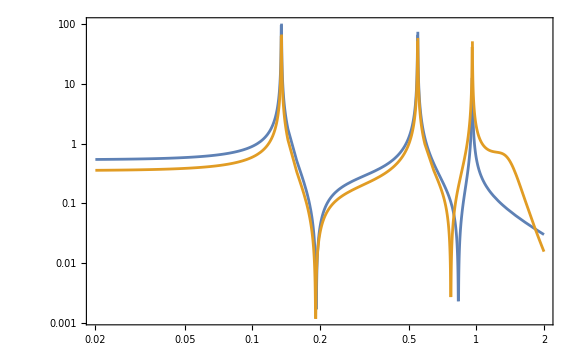

```mathematica
exprBlinov1[ma_,fa_]=((2 mη^2-5 mηpr^2+3 mπ0^2)*(6*DD*(ma^2-mη^2)+DDs*(9*ma^2-8 mη^2-mηpr^2)+2F*(mη^2-mηpr^2)))/(54fa*(ma^2-mη^2)(ma^2-mηpr^2));
(*3.45b - wih replaced mπ0->ma in some places*)
exprBlinov2[ma_,fa_]=(δ*mπ0^2((DD+F)(2 mη^2+mηpr^2-3 ma^2)*(2 mη^2-5 mηpr^2+3 mπ0^2))/(54*fa*(ma^2-mπ0^2)(ma^2-mη^2)(ma^2-mηpr^2)));
exprBlinov21[ma_,fa_]=(δ*mπ0^2((DD+F)(2 mη^2+mηpr^2-3 mπ0^2)*(2 mη^2-5 mηpr^2+3 mπ0^2))/(54*fa*(ma^2-mπ0^2)(mπ0^2-mη^2)(mπ0^2-mηpr^2)));
Print["g_app, {δ→0 term,~δ term}:"]
Print["Blinov (2112.09814, Eq. 3.45):"]
blinovsExpr=((#[ma,fa]/.{mηpr^2->M2relationPureChPT["η'"]}//Simplify)/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2})&/@{exprBlinov1,exprBlinov2}
Print["Maksym (2501.04525, Eq. B.39):"]
{gaNNexplicit[ma,0,0,0,1,fπ/fa]/.{δ->0}//Simplify,δ*D[gaNNexplicit[ma,0,0,0,1,fπ/fa],δ]//Simplify}
Print["Ta'el (2506.15637):"]
((#/.{m0^2->3(mη^2-mπ0^2)}/.{mηpr^2->M2relationPureChPT["η'"]}//Together//Simplify)/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2})&/@{(-m0^2*(2F+DDs))/(9fa*(ma^2-mη^2))+(-2 m0^2*(3DD-F+4DDs))/(9fa*(ma^2-mηpr^2)),(δ*mπ0^2*(DD+F)*m0^2((ma^2-mηpr^2)+2*(ma^2-mη^2)))/(9*fa*(ma^2-mπ0^2)(ma^2-mη^2)(ma^2-mηpr^2))}
FormFactorBrem[mS_]=Abs[With[{γ=0.515,δ=0.397,Γa1=0.4,ma1=1.36,α=0.95},Abs[1/(1-γ*Exp[I*δ]*mS^2)*(1-α+α*(ma1^2 (ma1^2-mS^2-I*ma1*Γa1))/((ma1^2-mS^2)^2+ma1^2*Γa1^2))]//ComplexExpand//Simplify]];
gaNNblinovRepl[ma_,fa_]=ruleSymbolsToNumbersFinal[blinovsExpr//Total,2]/.{F->0.46,DD->0.8,DDs->-0.41}//Simplify;
gaNNblinov[ma_,fa_]=ruleSymbolsToNumbersFinal[Total[{exprBlinov1[ma,fa],exprBlinov21[ma,fa]}],2]/.{F->0.46,DD->0.8,DDs->-0.41}//Simplify;
LogLogPlot[{Abs[gaNNnumeric[ma,0,0,0,1,1]],Abs[FormFactorBrem[ma]*gaNNblinov[ma,1]]},{ma,0.02,2},PlotRange->All,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20]]
```

### Exporting various couplings

## ALP decay widths

### a→ηπ^+π^- - scalar-mediated part

#### σ contribution

```mathematica
exprσMy=FeynmanRuleVertex0[{"a","σ","η"},{1,-1,-1},{"a","σ","3"}]*FeynmanRuleVertex0[{"σ","π^+","π^-"},{1,-1,-1},{"σ","1","2"}]/.{cG->0,δ->0}//Simplify;
{coefηALPmy,coefηprALPmy}=D[exprσMy,#]&/@{ηALP,ηprALP};
exprσSalvioni=-√2 ϵ*γσππ*(2γσηη*ηALP+γσηprηpr*ηprALP)*ScalarProduct[pa,p3]*ScalarProduct[p1,p2];
{coefηALPsalvioni,coefηprALPsalvioni}=D[exprσSalvioni,#]&/@{ηALP,ηprALP};
col1={"My",coefηALPmy,coefηprALPmy}/.{θs->θS,CoefA->Aval,CoefB->Bval,CoefC->Cval,CoefD->Dval};
col2={"Salvioni",coefηALPsalvioni,coefηprALPsalvioni}/.{γσηη->gNumber["σηη"],γσηprηpr->gNumber["σηprηpr"],γσππ->gNumber["σππ"]};
{{"Calculation","C_aη","C_aη'"},col1,col2}
```

(Calculation | C_aη | C_aη'
My | -63.8525 ϵ (OverBar[p1]·OverBar[p2]) (OverBar[p3]·OverBar[pa]) | -14.6978 ϵ (OverBar[p1]·OverBar[p2]) (OverBar[p3]·OverBar[pa])
Salvioni | -109.931 ϵ (OverBar[p1]·OverBar[p2]) (OverBar[p3]·OverBar[pa]) | 22.9003 ϵ (OverBar[p1]·OverBar[p2]) (OverBar[p3]·OverBar[pa]))

```mathematica
(109/63.)^2
```

2.99345

#### a_0 contribution

```mathematica
expra0My=FeynmanRuleVertex0[{"a","(a^+)_0","π^-"},{1,-1,-1},{"a","a0","2"}]*FeynmanRuleVertex0[{"(a^+)_0","π^+","η"},{1,-1,-1},{"σ","1","3"}]/.{cG->0,δ->0}//Simplify;
{coefηALPmy,coefηprALPmy}=D[expra0My,#]&/@{ηALP,ηprALP};
expra0Salvioni=-ϵ*γa0πη*(γa0πη*ηALP+γa0πηpr*ηprALP)*ScalarProduct[pa,p2]*ScalarProduct[p1,p3];
{coefηALPsalvioni,coefηprALPsalvioni}=D[expra0Salvioni,#]&/@{ηALP,ηprALP};
col1={"My",coefηALPmy,coefηprALPmy}/.{θs->θS,CoefA->Aval,CoefB->Bval,CoefC->Cval,CoefD->Dval};
col2={"Salvioni",coefηALPsalvioni,coefηprALPsalvioni}/.{γa0πη->gNumber["a0πη"],γa0πηpr->gNumber["a0πηpr"],γσππ->gNumber["σππ"]};
{{"Calculation","C_aη","C_aη'"},col1,col2}
```

(Calculation | C_aη | C_aη'
My | -42.0828 ϵ (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[pa]) | -54.5333 ϵ (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[pa])
Salvioni | -52.9941 ϵ (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[pa]) | -53.6979 ϵ (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[pa]))

### a->3π - scalar-mediated part

```mathematica
expr1=FeynmanRuleVertex0[{"a","σ","π^0"},{1,-1,-1},{"a","a0","3"}]*FeynmanRuleVertex0[{"σ","π^+","π^-"},{1,-1,-1},{"σ","1","2"}]/.{cG->0,δ->0}//Simplify
expr1/.{CoefA->Aval,CoefB->Bval,θs->θS}
-2*gNumber["σππ"]^2*ϵ
```

π0ALP (-ϵ) (OverBar[p1]·OverBar[p2]) (OverBar[p3]·OverBar[pa]) (√2 (CoefA-CoefB) cos(θs)+2 CoefB sin(θs))^2

-73.2023 π0ALP ϵ (OverBar[p1]·OverBar[p2]) (OverBar[p3]·OverBar[pa])

-146.405 ϵ

```mathematica
gNumber["σππ"]
```

8.55583

## Invisible π^0/η/η' decays

```mathematica
appr="O(δ,ϵ)";
Do[
appr="O(δ,ϵ)";
cm0a[meson,ma_,cu_,cd_,cs_,cG_,ϵ_]=D[m0aTransformation["a",x,appr],PfieldSymbol[meson,x]];
,{meson,listMesonP0}]
```

```mathematica
fff=cm0a["π^0",ma,OverBar[cu],OverBar[cd],OverBar[cs],-1/2 OverBar[cG],ϵ]/.{mηpr^2->M2relationPureChPT["η'"]}
1/ϵ D[fff,OverBar[cu]]/mπ0^2(ma^2-mπ0^2)/.{δ->0}
1/ϵ D[D[fff,OverBar[cu]]/mπ0^2(ma^2-mπ0^2),δ]//Simplify
```

(OverBar[cG] ((4 δ mπ0^2 ϵ (mη^2-mπ0^2))/(3 (mπ0^2-mη^2))+1/3 δ mπ0^2 ϵ))/(2 (ma^2-mπ0^2))-((2 δ mπ0^4 ϵ (OverBar[cd]-OverBar[cs]+OverBar[cu]))/(3 (mπ0^2-mη^2))+(δ mπ0^4 ϵ (OverBar[cd]+2 OverBar[cs]+OverBar[cu]))/(3 (4 mπ0^2-4 mη^2))-mπ0^2 ϵ (OverBar[cu]-OverBar[cd]))/(ma^2-mπ0^2)

1

(3 mπ0^2)/(4 (mη^2-mπ0^2))

```mathematica
fff=cm0a["η",ma,OverBar[cu],OverBar[cd],OverBar[cs],-1/2 OverBar[cG],ϵ]/.{mηpr^2->M2relationPureChPT["η'"]}
1/ϵ √(3/2)(ma^2-mη^2)D[fff,OverBar[cu]]/.{δ->0}
1/ϵ √(3/2)(ma^2-mη^2)D[D[fff,OverBar[cu]],δ]//Simplify
```

(OverBar[cG] (√(2/3) ϵ (mπ0^2-2 mη^2)+√(2/3) mη^2 ϵ))/(2 (ma^2-mη^2))-(-√(2/3) mη^2 ϵ (OverBar[cd]-OverBar[cs]+OverBar[cu])-(√(2/3) δ mη^2 mπ0^2 ϵ (OverBar[cd]-OverBar[cu]))/(mη^2-mπ0^2))/(ma^2-mη^2)

mη^2

-(mη^2 mπ0^2)/(mη^2-mπ0^2)

```mathematica
D[fff,OverBar[cG]]//Simplify
```

(δ mπ0^2 ϵ)/(2 ma^2-2 mπ0^2)

ϵ

(7 mπ0^2-4 mη^2)/(mη^2-mπ0^2)

```mathematica
fff=cm0a["η",ma,-OverBar[cu],-OverBar[cd],-OverBar[cs],-OverBar[cG]/2+(OverBar[cu]+OverBar[cd]+OverBar[cs]),ϵ]/.{mηpr^2->M2relationPureChPT["η'"]}
D[fff,OverBar[cu]](ma^2-mη^2)√(3/2)//Simplify
D[fff,OverBar[cu]](ma^2-mη^2)√(3/2)/.{δ->0}//Simplify
```

-((√(2/3) ϵ (mπ0^2-2 mη^2)+√(2/3) mη^2 ϵ) (OverBar[cd]-OverBar[cG]/2+OverBar[cs]+OverBar[cu]))/(ma^2-mη^2)-(-√(2/3) mη^2 ϵ (-OverBar[cd]+OverBar[cs]-OverBar[cu])-(√(2/3) δ mη^2 mπ0^2 ϵ (OverBar[cu]-OverBar[cd]))/(mη^2-mπ0^2))/(ma^2-mη^2)

(mπ0^2 ϵ ((δ-1) mη^2+mπ0^2))/(mη^2-mπ0^2)

-mπ0^2 ϵ

```mathematica
fff=cm0a["η'",ma,OverBar[cu],OverBar[cd],OverBar[cs],-OverBar[cG]/2-(OverBar[cu]+OverBar[cd]+OverBar[cs]),ϵ]/.{mηpr^2->M2relationPureChPT["η'"]}
D[fff,OverBar[cu]](ma^2-mη^2)√(3/2)//Simplify
D[fff,OverBar[cu]](ma^2-M2relationPureChPT["η'"])√(3/2)/.{δ->0}//Simplify
```

(ϵ (4 mη^2-4 mπ0^2) (-OverBar[cd]-OverBar[cG]/2-OverBar[cs]-OverBar[cu]))/(√3 (ma^2-4 mη^2+3 mπ0^2))-(-(ϵ (OverBar[cd] (4 mη^2-3 mπ0^2)+(4 mη^2-3 mπ0^2) (2 OverBar[cs]+OverBar[cu])))/(√3)-(δ mπ0^2 ϵ (4 mη^2-3 mπ0^2) (OverBar[cd]-OverBar[cu]))/(√3 (4 mη^2-4 mπ0^2)))/(ma^2-4 mη^2+3 mπ0^2)

-(ϵ (ma^2-mη^2) (4 (δ-1) mη^2 mπ0^2+(4-3 δ) mπ0^4))/(4 √2 (mη^2-mπ0^2) (ma^2-4 mη^2+3 mπ0^2))

(mπ0^2 ϵ)/(√2)

```mathematica
M2relationPureChPT["η'"]
```

4 mη^2-3 mπ0^2

```mathematica
cm0a["η'",ma,OverBar[cu],OverBar[cd],OverBar[cs],OverBar[cG]-2(OverBar[cu]+OverBar[cd]+OverBar[cs]),ϵ]
```

(ϵ (mηpr^2-mπ0^2) (OverBar[cG]-2 (OverBar[cd]+OverBar[cs]+OverBar[cu])))/(√3 (ma^2-mηpr^2))-(-(ϵ (mηpr^2 OverBar[cd]+mηpr^2 (2 OverBar[cs]+OverBar[cu])))/(√3)-(δ mηpr^2 mπ0^2 ϵ (OverBar[cd]-OverBar[cu]))/(√3 (mηpr^2-mπ0^2)))/(ma^2-mηpr^2)

```mathematica
mηpr^2->M2relationPureChPT["η'"]
```

mηpr^2→4 mη^2-3 mπ0^2

```mathematica
appr="O(δ,ϵ)";
Do[
appr="O(δ,ϵ)";
cm0a[meson,ma_,cu_,cd_,cs_,cG_,ϵ_]=D[m0aTransformation["a",x,appr],PfieldSymbol[meson,x]];
,{meson,listMesonP0}]
```

```mathematica
Do[
appr="O(δ,ϵ)";
cm0a[meson,ma_,cu_,cd_,cs_,cG_,ϵ_]=D[m0aTransformation["a",x,appr],PfieldSymbol[meson,x]];
Mel=cm0alp*gχ*SpinorUBar[pχ1,mχ].GA5.SpinorV[pχ2,mχ];
Mel2=FermionSpinSum[Mel*ComplexConjugate[Mel]]/.{DiracTrace->TR}/.{ScalarProduct[pχ1,pχ2]->(msymbolic[meson]^2-2*mχ^2)/2}//Simplify;
ΓmesonToInv[meson,ma_,mχ_,cu_,cd_,cs_,cG_,fπ_,fa_,gχ_]=1/(8*Pi)Mel2*(√(msymbolic[meson]^2-4*mχ^2))/(2*msymbolic[meson]^2)/.{cm0alp->cm0a[meson,ma,cu,cd,cs,cG,fπ/fa]}//Simplify;
ΓmesonToInvGluon[meson,ma_,mχ_,cG_,fπ_,fa_,gχ_]=ΓmesonToInv[meson,ma,mχ,0,0,0,cG,fπ,fa,gχ];
BrmesonToInvGluonNum[meson,ma_,mχ_,cG_,fa_,gχ_]=ΓmesonToInvGluon[meson,ma,mχ,cG,Fπ,fa,gχ]/DECAYWIDTH[meson]/.Table[msymbolic[meson]->MASS[meson],{meson,listMesonP0}]/.{δ->δval};
boundALPmesonToInvGluon[meson,BrInv_,ma_,mχ_,gχ_]=If[MASS[meson]>2mχ,Evaluate[(√(BrmesonToInvGluonNum[meson,ma,mχ,1,1,gχ]/BrInv))^-1],10.]
,{meson,listMesonP0}];
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"auxiliary data","ALP-meson-mixing.m"}],{#,cm0a[#,ma,cu,cd,cs,cG,fπ/fa]}&/@listMesonP0,"MX"]
MALPdecInv=gχ*SpinorUBar[pχ1,mχ].GA5.SpinorV[pχ2,mχ]
MALPdecInv2=FermionSpinSum[MALPdecInv*ComplexConjugate[MALPdecInv]]/.{DiracTrace->TR}/.{DiracTrace->TR}/.{ScalarProduct[pχ1,pχ2]->(ma^2-2*mχ^2)/2}//Simplify;
ΓALPToInv[ma_,mχ_,gχ_]=1/(8*Pi)MALPdecInv2*(√(ma^2-4*mχ^2))/(2*ma^2)//Simplify;
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\New\auxiliary data\ALP-meson-mixing.m

gχ ū(pχ1,mχ).(γ̄)^5.v(pχ2,mχ)

```mathematica
BrmesonToInvGluonNum["π^0",ma,cG,fa,gχ]
```

(0.0360443 cG^2 gχ^2 √(0.018225-4 mχ^2))/(fa^2 (ma^2-0.018225)^2)

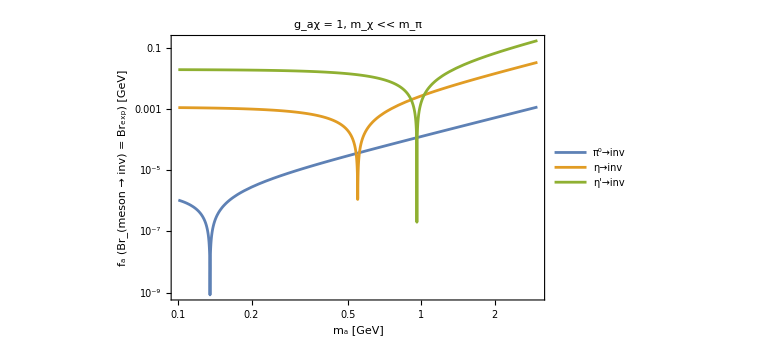

```mathematica
LogLogPlot[{(√(BrmesonToInvGluonNum["π^0",ma,0.001,1,1,1]/(4.4*10^-9)))^-1,(√(BrmesonToInvGluonNum["η",ma,0.001,1,1,1]/(1.1*10^-4)))^-1,(√(BrmesonToInvGluonNum["η'",ma,0.001,1,1,1]/(2.1*10^-4)))^-1},{ma,0.1,3},Frame->True,FrameStyle->Directive[Thick,Black,20],ImageSize->Large,PlotLegends->Placed[Style[Row[{#}],20,Black]&/@{"π^0→inv","η→inv","η'→inv"}, {0.8,0.2}],PlotLabel->Style[Row[{"g_aχ = 1, m_χ << m_π"}],20,Black],FrameLabel->{"m_a [GeV]","f_a (Br_(meson → inv) = Br_exp) [GeV]"}]
```

```mathematica
ALPdecayWidthVisibleDat[[4]][[1]]
```

{m_a, GeV,2e,2γ,2μ,2τ,2b,2c,2d,2G,2s,2t,2u,2K_Lπ^0,2K_Sπ^0,2ηπ^0,2π^+2π^-,2ρ^0,2ϕ,2ω,3π^0,3η,K_LK_Sπ^0,K^(*0)(K̄)^(*0),K^-K_Lπ^+,K^+K_Lπ^-,K^-K_Sπ^+,K^+K_Sπ^-,K^(*+)K^(*-),K^+K^-π^0,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ρ^+ρ^-,ωπ^+π^-,η'2π^0,η'π^+π^-,Non-hadronic, total,Hadronic, total,Total}

```mathematica
ALPinv=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"auxiliary data","sigma-ALP-set-I.txt"}],"Table"];
ALPdecayWidthVisibleDat=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology","Gluon","decays","Widths-model-Gluon-scale-1000.-GeV.m"}],"MX"];
ALPdecayWidthVisible[ma_,fa_]=fa^-2 Interpolation[Drop[ALPdecayWidthVisibleDat[[4]][[All,{1,-1}]],4],InterpolationOrder->1][ma];
NevALPinvRealistic[ma_,mχ_,fa_,gχ_]=fa^-2 10^17.(Interpolation[ALPinv[[All,{1,3}]]//Log,InterpolationOrder->1][Log[ma]]//Exp)*(ΓALPToInv[ma,mχ,gχ]/(ALPdecayWidthVisible[ma,fa]+ΓALPToInv[ma,mχ,gχ]));
SensitivityALPinvRealistic[ma_,mχ_,gχ_]=(fa/.Solve[NevALPinvRealistic[ma,mχ,fa,gχ]==2.3,fa][[2]])^-1;
```

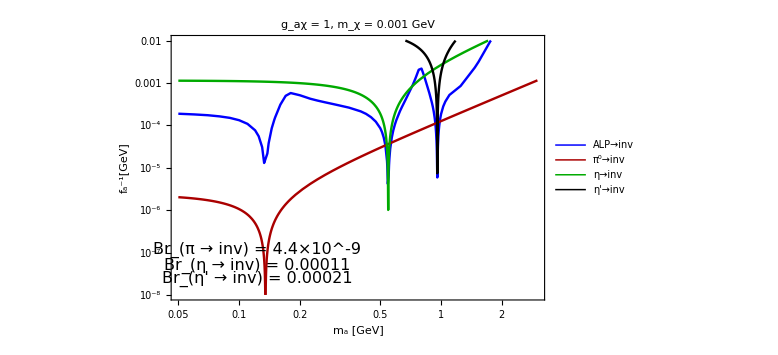
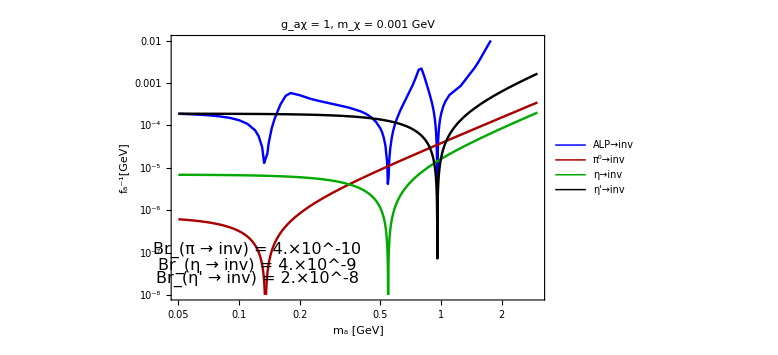

```mathematica
plotFin[gχ_,mχ_,BrInvπ_,BrInvη_,BrInvηPr_]:=Block[{},
modelDef1=Graphics[{Inset[Style[Row[{"Br_(π → inv) = ",BrInvπ}],FontSize->16,FontFamily->"Palatino",FontColor->Black],Scaled[{0.23,0.19}],Center]}];
modelDef2=Graphics[{Inset[Style[Row[{"Br_(η → inv) = ",BrInvη}],FontSize->16,FontFamily->"Palatino",FontColor->Black],Scaled[{0.23,0.13}],Center]}];
modelDef3=Graphics[{Inset[Style[Row[{"Br_(η' → inv) = ",BrInvηPr}],FontSize->16,FontFamily->"Palatino",FontColor->Black],Scaled[{0.23,0.08}],Center]}];
pt1=LogLogPlot[Evaluate[{SensitivityALPinvRealistic[ma,mχ,gχ],boundALPmesonToInvGluon["π^0",BrInvπ,ma,mχ,gχ],boundALPmesonToInvGluon["η",BrInvη,ma,mχ,gχ],boundALPmesonToInvGluon["η'",BrInvηPr,ma,mχ,gχ]}],{ma,0.05,3},PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"ALP→inv","π^0→inv","η→inv","η'→inv"}, {0.85,0.2}],Frame->True,FrameStyle->Directive[Thick,"Palatino",Bold,Black,20,FontFamily->"Palatino"],PlotRange->{{0.05,3},{10^-8.,10^-2}},ImageSize->Large,PlotLabel->Style[Row[{"g_aχ = ",gχ,", m_χ = ",mχ," GeV"}],20,Black,FontFamily->"Palatino"],FrameLabel->{"m_a [GeV]",Row[{Subsuperscript["f","a","-1"], "[GeV]"}]},PlotStyle->({Thickness[0.003],#}&/@{Blue,Darker@Red,Darker@Green,Black})];
Show[pt1,modelDef1,modelDef2,modelDef3]
]
ptshow1=plotFin[1,10^-3.,4.4*10^-9,1.1*10^-4,2.1*10^-4];
ptshow2=plotFin[1,10^-3.,4.*10^-10,4.*10^-9,2.*10^-8];
Style[Row[{ptshow1,ptshow2}],ImageSizeMultipliers->{1, 1}]
ptshow3=plotFin[0.1,10^-3.,4.4*10^-9,1.1*10^-4,2.1*10^-4];
ptshow4=plotFin[0.1,10^-3.,4.*10^-10,4.*10^-9,2.*10^-8];
Style[Row[{ptshow3,ptshow4}],ImageSizeMultipliers->{1, 1}]
ptshow5=plotFin[1,ma/3,4.4*10^-9,1.1*10^-4,2.1*10^-4];
ptshow6=plotFin[1,ma/3,4.*10^-10,4.*10^-9,2.*10^-8];
Style[Row[{ptshow5,ptshow6}],ImageSizeMultipliers->{1, 1}]
```

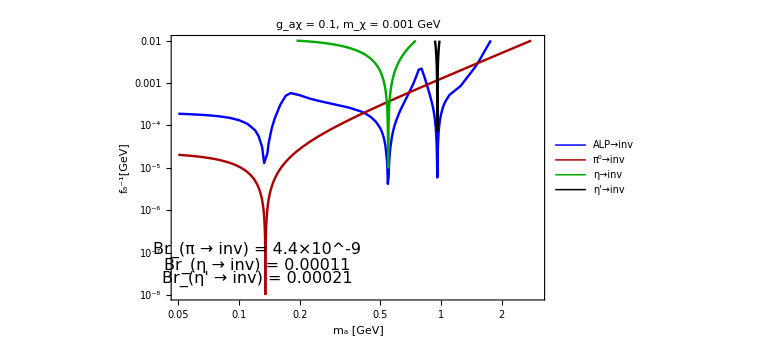
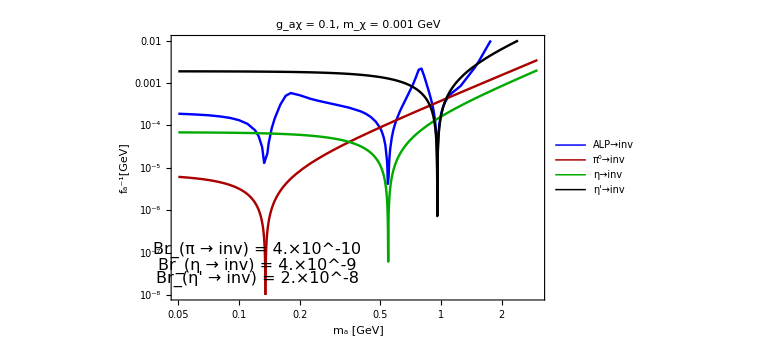

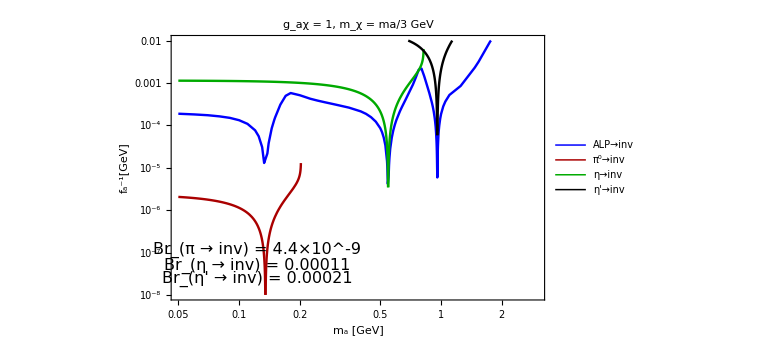
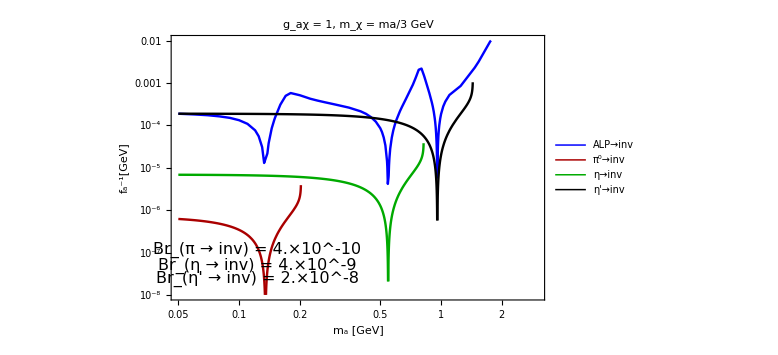

```mathematica
boundALPmesonToInvGluon["η",BrInvπ,0.3,0.3/3,gχ]
```

0.0788505/(√(gχ^2/BrInvπ))